```mathematica
Clear[s,i,α]
L=6;
Monitor[
Table[s[i,α]=KroneckerProduct[SparseArray[IdentityMatrix[2^(i-1)]],SparseArray[PauliMatrix[α]/2],SparseArray[IdentityMatrix[2^(L-i)]]],{i,1,L},{α,0,3}],i];
```

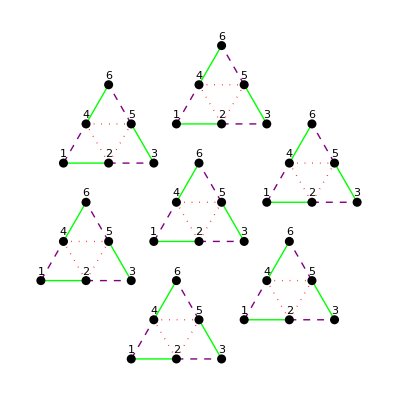

```mathematica
ϕ=-π/6;
δ1={Cos[ϕ],Sin[ϕ]};
δ2={Cos[ϕ],-Sin[ϕ]};
δ1={1,0};
δ2=1/2{1,√3};
coords={0δ1,δ1,2δ1,δ2,δ2+δ1,2δ2};
(* intra-UC interactions *)
j1s={{2,3},{1,4},{5,6}};
j2s={{1,2},{3,5},{4,6}};
j3s={{2,4},{2,5},{4,5}};

p=Disk[#,0.1]&/@coords;
l=Table[Text[Style[ToString[i],Black],coords[[i]]+{0,0.2}],{i,Length[coords]}];
lj1={Dashed,Purple,Line[coords[[#]]]}&/@j1s;
lj2={Green,Line[coords[[#]]]}&/@j2s;
lj3={Dotted,Red,Line[coords[[#]]]}&/@j3s;
uc={lj1,lj2,lj3,p,l};

a1=2δ1+δ2;
a2=3δ1-2δ2;

(* inter-UC connections [used to implement pbcs later] *)
j1pbcs={{1,5},{5,1},{2,6},{6,2},{3,4},{4,3}};
j3pbcs={{1,3},{3,1},{1,6},{6,1},{3,6},{6,3}};

Graphics[{uc,Translate[uc,a1],Translate[uc,a1-a2],Translate[uc,a2],Translate[uc,-a1+a2],Translate[uc,-a1],Translate[uc,-a2]},Axes->False]
```

```mathematica
Clear[j3,j1,j2,pbc]
HC[j1_,j2_,j3_,pbc_]:=Sum[
+j1*s[j1c[[1]],α].s[j1c[[2]],α]
,{α,3},{j1c,j1s}]+
Sum[
+j2*s[j2c[[1]],α].s[j2c[[2]],α]
,{α,3},{j2c,j2s}]+
Sum[
+j3*s[j3c[[1]],α].s[j3c[[2]],α]
,{α,3},{j3c,j3s}]+
(* PBC terms *)
pbc*Sum[
+j1*s[j1c[[1]],α].s[j1c[[2]],α]
,{α,3},{j1c,j1pbcs}]+
pbc*Sum[
+j3*s[j3c[[1]],α].s[j3c[[2]],α]
,{α,3},{j3c,j3pbcs}];
```

```mathematica
Tally[Eigensystem[HC[0.,0,1,0]][[1]]//Sort,Abs[#1-#2]<10^-6&]
```

{{-0.75,32},{0.75,32}}

```mathematica
j2vs=Table[j//N,{j,-2,2,0.01}];
es=Eigensystem[HC[1.,#,1,0]]&/@j2vs;
```

```mathematica
vals = Sort[#/6]&/@es[[;;,1]];
```

```mathematica
<<MaTeX`
```

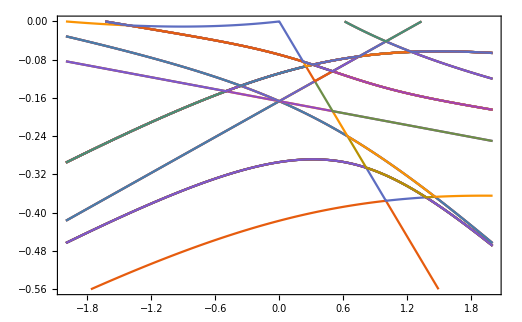

```mathematica
ListPlot[valsᵀ,Joined->True,DataRange->{-2,2},PlotTheme->"Scientific",GridLines->{{1,1.39,1.47},{-3/8}},PlotRange->{-0.56,0},FrameLabel->MaTeX[{"J_2","E/N"}]]
```

```mathematica
vals[[1]]
```

{-0.375,-0.375,-0.321789,-0.321789,-0.321789,-0.321789,-0.321789,-0.321789,-0.291667,-0.291667,-0.291667,-0.208333,-0.208333,-0.138954,-0.138954,-0.138954,-0.138954,-0.138954,-0.138954,-0.066898,-0.066898,-0.066898,-0.066898,-0.066898,-0.066898,-0.066898,-0.066898,-0.066898,-0.066898,-0.0416667,-0.0416667,-0.0416667,-0.0416667,-0.0416667,-0.0416667,0.0416667,0.0416667,0.0416667,0.0416667,0.0416667,0.0416667,0.0857432,0.0857432,0.0857432,0.0857432,0.0857432,0.0857432,0.233565,0.233565,0.233565,0.233565,0.233565,0.233565,0.233565,0.233565,0.233565,0.233565,0.375,0.375,0.375,0.375,0.375,0.375,0.375}

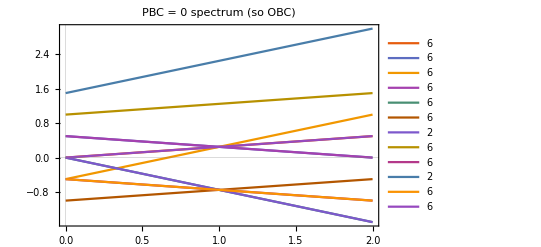

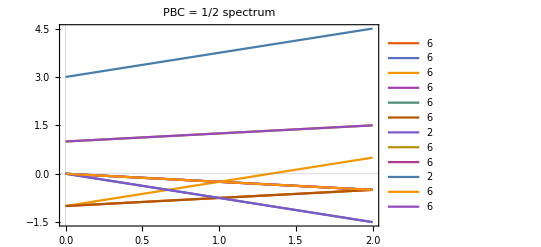

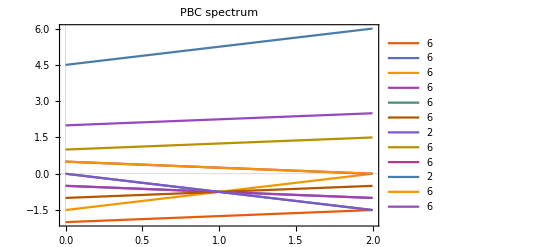

```mathematica
spec = Tally[vals];
Plot[Evaluate[spec[[;;,1]]/.{j3->1,j1->1,pbc->0}],{j2,0,2},PlotTheme->"Scientific",PlotLegends->spec[[;;,2]],PlotLabel->"PBC = 0 spectrum (so OBC)"]
Plot[Evaluate[spec[[;;,1]]/.{j3->1,j1->1,pbc->1/2}],{j2,0,2},PlotTheme->"Scientific",PlotLegends->spec[[;;,2]],PlotLabel->"PBC = 1/2 spectrum"]
Plot[Evaluate[spec[[;;,1]]/.{j3->1,j1->1,pbc->1}],{j2,0,2},PlotTheme->"Scientific",PlotLegends->spec[[;;,2]],PlotLabel->"PBC spectrum"]
```